# Dynamical Matrices for 3D Lattices

## Introduction - Monatomic Bases

To solve for the vibrational normal modes of a monatomic Bravais lattice, we assume a wavelike solution of the form:

U⃗ = ϵ⃗ E^(k⃗·(R⃗)_n- ω t)

By making a harmonic approximation and assuming atoms are connected by Hooke like interactions, the following Dynamical Matrix equation can be  recovered:

D̂ ϵ⃗ = ω^2 ϵ⃗

Therefore, if one can determine the dynamical matrix D̂, then it can be diagonalized to yield the vibrational frequencies (ω) and the polarizations (ϵ⃗). For a monatomic basis, this matrix is given by:

D̂(k⃗) = -2/m ∑_((R⃗)_n)Φ_OverVector[0]^((R⃗)_n)Sin[(k⃗ · (R⃗)_n)/2]

All that remains is to determine the generalized spring constants Φ. Since we do not need to determine Φ_OverVector[0]^OverVector[0] thanks to the sine term giving zero, then we can make use of the following equation:

(Φ_OverVector[0]^((R⃗)_n≠OverVector[0]))^(i j) = -f/a^2(r_((R⃗)_n)^i- r_OverVector[0]^i)(r_((R⃗)_n)^j- r_OverVector[0]^j)

Here, f is the spring constant of the individual springs connecting atoms and a is the nearest neighbor distance. This equation makes the assumption that only nearest neighbors are connected by springs, which we will assume from now on.

## Cubic Lattice - Coordination Number 6

```mathematica
(* Direct lattice vectors *)
a1 = {a, 0, 0};
a2 = {0, a, 0};
a3 = {0, 0, a};
```

```mathematica
(* Nearest neighbor locations, up to inversion symmetries *)
coordination = 6;
inversion = coordination / 2;
neighbors = Table[{0,0,0}, {n,1, inversion}];
neighbors[[1]] = a1;
neighbors[[2]] = a2;
neighbors[[3]] = a3;
(* Input no further! *)
```

```mathematica
(* Build generalized spring constants *)
generalizedphi = Table[{{0,0, 0},{0,0, 0}, {0, 0, 0}}, {n, 1, inversion}];
For[n=1,n≤ inversion,n++,
generalizedphi[[n]]=  -f/a^2 * Table[neighbors[[n]][[i]]×neighbors[[n]][[j]], {i, 1, 3}, {j, 1, 3}]; 
Print[generalizedphi[[n]] //MatrixForm];
]
```

(-f | 0 | 0
0 | 0 | 0
0 | 0 | 0)

(0 | 0 | 0
0 | -f | 0
0 | 0 | 0)

(0 | 0 | 0
0 | 0 | 0
0 | 0 | -f)

```mathematica
(* Construct reciprocal basis *)
vol = a1 . Cross[a2,a3];
b1 = 2 Pi Cross[a2 , a3] / vol;
b2 = 2Pi Cross[a3 , a1] / vol; 
b3 = 2 Pi Cross[a1 , a2] / vol;
```

```mathematica
(* Build dynamical matrix, times two for inversion symmetry *)
krecip= h b1 + k b2 + l b3;
dynam = {{0,0, 0},{0,0, 0}, {0, 0, 0}};
For[n=1,n≤ inversion,n++,
dynam=dynam +-4/m generalizedphi[[n]]× Sin[(krecip.neighbors[[n]])/2]^2;
]
Print[Simplify[dynam] //MatrixForm];
```

((4 f Sin[h π]^2)/m | 0 | 0
0 | (4 f Sin[k π]^2)/m | 0
0 | 0 | (4 f Sin[l π]^2)/m)

```mathematica
(* Determine polarizations and frequencies *)
{evals, evecs} = Eigensystem[dynam];
{ω1, ω2, ω3} = Sqrt[evals];
{ϵ1, ϵ2, ϵ3} = evecs;
Print[ϵ1 // MatrixForm, ω1];
Print[ϵ2 // MatrixForm, ω2];
Print[ϵ3 // MatrixForm, ω3];
```

(1
0
0)2 √((f Sin[h π]^2)/m)

(0
1
0)2 √((f Sin[k π]^2)/m)

(0
0
1)2 √((f Sin[l π]^2)/m)

## BCC Lattice - Coordination Number 8

The slight change here is that even though a = conventional unit cell length, it no longer respects a = nearest neighbor distance.

```mathematica
(* Direct lattice vectors *)
a1 = a/2×{-1, 1, 1};
a2 = a/2×{1, -1, 1};
a3 = a/2×{1, 1, -1};
```

```mathematica
(* Nearest neighbor locations, up to inversion symmetries *)
coordination = 8;
inversion = coordination / 2;
neighbors = Table[{0,0,0}, {n,1, inversion}];
neighbors[[1]] = a1;
neighbors[[2]] = a2;
neighbors[[3]] = a3;
neighbors[[4]] = a1 + a2 + a3;
(* Input no further! *)
```

```mathematica
(* Build generalized spring constants *)
generalizedphi = Table[{{0,0, 0},{0,0, 0}, {0, 0, 0}}, {n, 1, inversion}];
abcc = Sqrt[3]/2 a;
For[n=1,n≤ inversion,n++,
generalizedphi[[n]]=  -f/abcc^2 * Table[neighbors[[n]][[i]]×neighbors[[n]][[j]], {i, 1, 3}, {j, 1, 3}]; 
Print[generalizedphi[[n]] //MatrixForm];
]
```

(-f/3 | f/3 | f/3
f/3 | -f/3 | -f/3
f/3 | -f/3 | -f/3)

(-f/3 | f/3 | -f/3
f/3 | -f/3 | f/3
-f/3 | f/3 | -f/3)

(-f/3 | -f/3 | f/3
-f/3 | -f/3 | f/3
f/3 | f/3 | -f/3)

(-f/3 | -f/3 | -f/3
-f/3 | -f/3 | -f/3
-f/3 | -f/3 | -f/3)

```mathematica
(* Construct reciprocal basis *)
vol = a1 . Cross[a2,a3];
b1 = 2 Pi Cross[a2 , a3] / vol;
b2 = 2Pi Cross[a3 , a1] / vol; 
b3 = 2 Pi Cross[a1 , a2] / vol;
```

```mathematica
(* Build dynamical matrix, times two for inversion symmetry *)
krecip= h b1 + k b2 + l b3;
dynam = {{0,0, 0},{0,0, 0}, {0, 0, 0}};
For[n=1,n≤ inversion,n++,
dynam=dynam +-4/m generalizedphi[[n]]× Sin[(krecip.neighbors[[n]])/2]^2;
]
Print[Simplify[dynam] //MatrixForm];
```

(-(8 f (-1+Cos[(h+k) π] Cos[(h+l) π] Cos[(k+l) π]))/(3 m) | (8 f Cos[(h+k) π] Sin[(h+l) π] Sin[(k+l) π])/(3 m) | (8 f Cos[(h+l) π] Sin[(h+k) π] Sin[(k+l) π])/(3 m)
(8 f Cos[(h+k) π] Sin[(h+l) π] Sin[(k+l) π])/(3 m) | -(8 f (-1+Cos[(h+k) π] Cos[(h+l) π] Cos[(k+l) π]))/(3 m) | (8 f Cos[(k+l) π] Sin[(h+k) π] Sin[(h+l) π])/(3 m)
(8 f Cos[(h+l) π] Sin[(h+k) π] Sin[(k+l) π])/(3 m) | (8 f Cos[(k+l) π] Sin[(h+k) π] Sin[(h+l) π])/(3 m) | -(8 f (-1+Cos[(h+k) π] Cos[(h+l) π] Cos[(k+l) π]))/(3 m))

```mathematica
(* Determine polarizations and frequencies *)
{evals, evecs} = Eigensystem[dynam];
{ω1, ω2, ω3} = Simplify[Sqrt[evals]];
{ϵ1, ϵ2, ϵ3} = Simplify[evecs];
(* Print[ϵ1 // MatrixForm, ω1];
Print[ϵ2 // MatrixForm, ω2];
Print[ϵ3 // MatrixForm, ω3]; *)
```

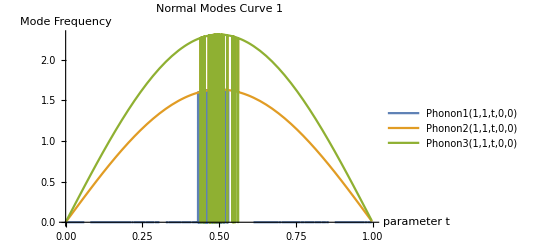

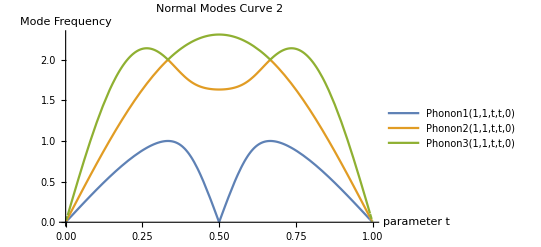

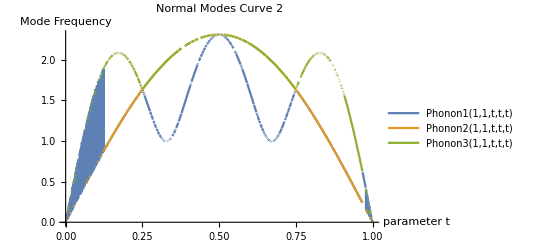

```mathematica
(* Plot dispersion relations *)
Phonon1[f_,m_,h_,k_,l_] = ω1;
Phonon2[f_,m_,h_,k_,l_] = ω2;
Phonon3[f_,m_,h_,k_,l_] = ω3;
Plot[{Phonon1[1,1 ,t,0,0], Phonon2[1,1,t,0,0], Phonon3[1,1,t,0,0]}, {t,0,1}, PlotLegends->"Expressions", PlotLabel -> "Normal Modes Curve 1", AxesLabel -> {"parameter t", "Mode Frequency"}]
Plot[{Phonon1[1,1 ,t,t,0], Phonon2[1,1,t,t,0], Phonon3[1,1,t,t,0]}, {t,0,1}, PlotLegends->"Expressions", PlotLabel -> "Normal Modes Curve 2", AxesLabel -> {"parameter t", "Mode Frequency"}]
Plot[{Phonon1[1,1 ,t,t,t], Phonon2[1,1,t,t,t], Phonon3[1,1,t,t,t]}, {t,0,1}, PlotLegends->"Expressions", PlotLabel -> "Normal Modes Curve 3", AxesLabel -> {"parameter t", "Mode Frequency"}]
```

## FCC Lattice - Coordination Number 12

```mathematica
(* Direct lattice vectors *)
a1 = a/2×{0, 1, 1};
a2 = a/2×{1, 0, 1};
a3 = a/2×{1, 1, 0};
```

```mathematica
(* Nearest neighbor locations, up to inversion symmetries *)
coordination = 12;
inversion = coordination / 2;
neighbors = Table[{0,0,0}, {n,1, inversion}];
neighbors[[1]] = a1;
neighbors[[2]] = a2;
neighbors[[3]] = a3;
neighbors[[4]] = a2 - a3;
neighbors[[5]] = a1 - a3;
neighbors[[6]] = a1 - a2;
(* Input no further! *)
```

```mathematica
(* Build generalized spring constants *)
generalizedphi = Table[{{0,0, 0},{0,0, 0}, {0, 0, 0}}, {n, 1, inversion}];
afcc = Sqrt[2]/2 a;
For[n=1,n≤ inversion,n++,
generalizedphi[[n]]=  -f/afcc^2 * Table[neighbors[[n]][[i]]×neighbors[[n]][[j]], {i, 1, 3}, {j, 1, 3}]; 
Print[generalizedphi[[n]] //MatrixForm];
]
```

(0 | 0 | 0
0 | -f/2 | -f/2
0 | -f/2 | -f/2)

(-f/2 | 0 | -f/2
0 | 0 | 0
-f/2 | 0 | -f/2)

(-f/2 | -f/2 | 0
-f/2 | -f/2 | 0
0 | 0 | 0)

(0 | 0 | 0
0 | -f/2 | f/2
0 | f/2 | -f/2)

(-f/2 | 0 | f/2
0 | 0 | 0
f/2 | 0 | -f/2)

(-f/2 | f/2 | 0
f/2 | -f/2 | 0
0 | 0 | 0)

```mathematica
(* Construct reciprocal basis *)
vol = a1 . Cross[a2,a3];
b1 = 2 Pi Cross[a2 , a3] / vol;
b2 = 2Pi Cross[a3 , a1] / vol; 
b3 = 2 Pi Cross[a1 , a2] / vol;
```

```mathematica
(* Build dynamical matrix, times two for inversion symmetry *)
krecip= h b1 + k b2 + l b3;
dynam = {{0,0, 0},{0,0, 0}, {0, 0, 0}};
For[n=1,n≤ inversion,n++,
dynam=dynam +-4/m generalizedphi[[n]]× Sin[(krecip.neighbors[[n]])/2]^2;
]
Print[Simplify[dynam] //MatrixForm];
```

(-(2 f (-2+Cos[(h+k-l) π] Cos[(-h+k+l) π]+Cos[(h-k+l) π] Cos[(-h+k+l) π]))/m | (2 f Sin[(h-k+l) π] Sin[(-h+k+l) π])/m | (2 f Sin[(h+k-l) π] Sin[(-h+k+l) π])/m
(2 f Sin[(h-k+l) π] Sin[(-h+k+l) π])/m | -(2 f (-2+Cos[(h+k-l) π] Cos[(h-k+l) π]+Cos[(h-k+l) π] Cos[(-h+k+l) π]))/m | (2 f Sin[(h+k-l) π] Sin[(h-k+l) π])/m
(2 f Sin[(h+k-l) π] Sin[(-h+k+l) π])/m | (2 f Sin[(h+k-l) π] Sin[(h-k+l) π])/m | -(2 f (-2+Cos[(h+k-l) π] (Cos[(h-k+l) π]+Cos[(-h+k+l) π])))/m)

```mathematica
(* Determine polarizations and frequencies *)
{evals, evecs} = Eigensystem[dynam];
{ω1, ω2, ω3} = Simplify[Sqrt[evals]];
{ϵ1, ϵ2, ϵ3} = Simplify[evecs];
(* Print[ϵ1 // MatrixForm, ω1];
Print[ϵ2 // MatrixForm, ω2];
Print[ϵ3 // MatrixForm, ω3]; *)
```

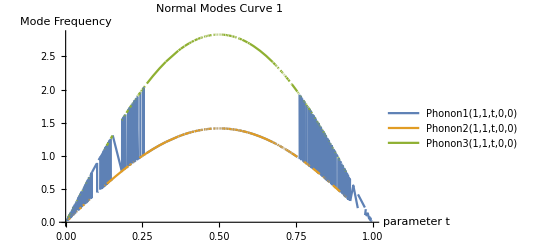

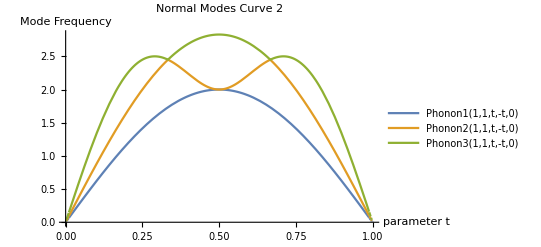

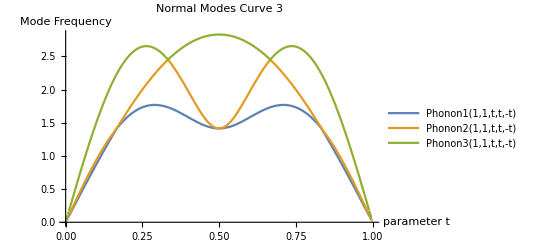

```mathematica
(* Plot dispersion relations *)
Phonon1[f_,m_,h_,k_,l_] = ω1;
Phonon2[f_,m_,h_,k_,l_] = ω2;
Phonon3[f_,m_,h_,k_,l_] = ω3;
Plot[{Phonon1[1,1 ,t,0,0], Phonon2[1,1,t,0,0], Phonon3[1,1,t,0,0]}, {t,0,1}, PlotLegends->"Expressions", PlotLabel -> "Normal Modes Curve 1", AxesLabel -> {"parameter t", "Mode Frequency"}]
Plot[{Phonon1[1,1 ,t,-t,0], Phonon2[1,1,t,-t,0], Phonon3[1,1,t,-t,0]}, {t,0,1}, PlotLegends->"Expressions", PlotLabel -> "Normal Modes Curve 2", AxesLabel -> {"parameter t", "Mode Frequency"}]
Plot[{Phonon1[1,1 ,t,t,-t], Phonon2[1,1,t,t,-t], Phonon3[1,1,t,t,-t]}, {t,0,1}, PlotLegends->"Expressions", PlotLabel -> "Normal Modes Curve 3", AxesLabel -> {"parameter t", "Mode Frequency"}]
```

## Sanity Check - FCC (111) Plane - Coordination Number 6

To ensure our framework is functional, we can consider the FCC crystal with only the nearest neighbors that compose the (111) plane. In this case, we simply model a 2D hexagonal lattice, and therefore upon diagonalization, the polarizations and frequencies should match the results of the 2D hex lattice.

```mathematica
(* Direct lattice vectors *)
a1 = a/2×{0, 1, 1};
a2 = a/2×{1, 0, 1};
a3 = a/2×{1, 1, 0};
```

```mathematica
(* Nearest neighbor locations, up to inversion symmetries *)
coordination = 6;
inversion = coordination / 2;
neighbors = Table[{0,0,0}, {n,1, inversion}];
neighbors[[1]] = a1;
neighbors[[2]] = a2;
neighbors[[3]] = a1 - a2;
(* Input no further! *)
```

```mathematica
(* Build generalized spring constants *)
generalizedphi = Table[{{0,0, 0},{0,0, 0}, {0, 0, 0}}, {n, 1, inversion}];
afcc = Sqrt[2]/2 a;
For[n=1,n≤ inversion,n++,
generalizedphi[[n]]=  -f/afcc^2 * Table[neighbors[[n]][[i]]×neighbors[[n]][[j]], {i, 1, 3}, {j, 1, 3}]; 
Print[generalizedphi[[n]] //MatrixForm];
]
```

```mathematica
(* Construct reciprocal basis *)
vol = a1 . Cross[a2,a3];
b1 = 2 Pi Cross[a2 , a3] / vol;
b2 = 2Pi Cross[a3 , a1] / vol; 
b3 = 2 Pi Cross[a1 , a2] / vol;
```

```mathematica
(* Build dynamical matrix, times two for inversion symmetry *)
krecip= h b1 + k b2 + l b3;
dynam = {{0,0, 0},{0,0, 0}, {0, 0, 0}};
For[n=1,n≤ inversion,n++,
dynam=dynam +-4/m generalizedphi[[n]]× Sin[(krecip.neighbors[[n]])/2]^2;
]
Print[Simplify[dynam] //MatrixForm]
```

```mathematica
(* Determine polarizations and frequencies *)
{evals, evecs} = Eigensystem[dynam];
{ω1, ω2, ω3} = Simplify[Sqrt[evals]];
{ϵ1, ϵ2, ϵ3} = Simplify[evecs];
Print[ϵ1 // MatrixForm, ω1]
Print[ϵ2 // MatrixForm, ω2]
Print[ϵ3 // MatrixForm, ω3]
```

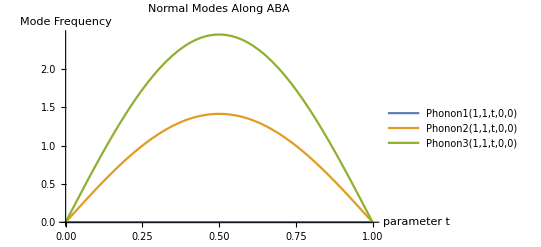

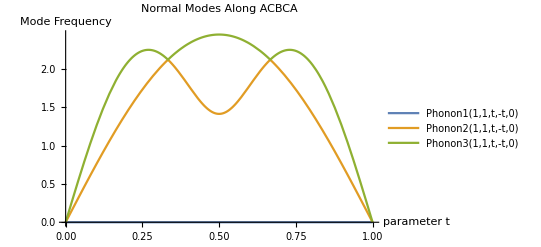

```mathematica
(* Plot dispersion relations *)
Phonon1[f_,m_,h_,k_,l_] = ω1;
Phonon2[f_,m_,h_,k_,l_] = ω2;
Phonon3[f_,m_,h_,k_,l_] = ω3;
Plot[{Phonon1[1,1 ,t,0,0], Phonon2[1,1,t,0,0], Phonon3[1,1,t,0,0]}, {t,0,1}, PlotLegends->"Expressions", PlotLabel -> "Normal Modes Along ABA", AxesLabel -> {"parameter t", "Mode Frequency"}]
Plot[{Phonon1[1,1 ,t,-t,0], Phonon2[1,1,t,-t,0], Phonon3[1,1,t,-t,0]}, {t,0,1}, PlotLegends->"Expressions", PlotLabel -> "Normal Modes Along ACBCA", AxesLabel -> {"parameter t", "Mode Frequency"}]
```

## Better Sanity Check - 2D Triangular Lattice - Coordination Number 6

Now we consider the easier 2D example of atoms only in the xy-plane

```mathematica
(* Direct lattice vectors *)
a1 = a ×{     1,                     0, 0};
a2 = a ×{1/2, Sqrt[3]/2, 0};
a3 = a ×{     0,                     0, 1};
```

```mathematica
(* Nearest neighbor locations, up to inversion symmetries *)
coordination = 6;
inversion = coordination / 2;
neighbors = Table[{0,0,0}, {n,1, inversion}];
neighbors[[1]] = a1;
neighbors[[2]] = a2;
neighbors[[3]] = a1 - a2;
(* Input no further! *)
```

```mathematica
(* Build generalized spring constants *)
generalizedphi = Table[{{0,0, 0},{0,0, 0}, {0, 0, 0}}, {n, 1, inversion}];
For[n=1,n≤ inversion,n++,
generalizedphi[[n]]=  -f/a^2 * Table[neighbors[[n]][[i]]×neighbors[[n]][[j]], {i, 1, 3}, {j, 1, 3}]; 
Print[generalizedphi[[n]] //MatrixForm];
]
```

(-f | 0 | 0
0 | 0 | 0
0 | 0 | 0)

(-f/4 | -(√3 f)/4 | 0
-(√3 f)/4 | -(3 f)/4 | 0
0 | 0 | 0)

(-f/4 | (√3 f)/4 | 0
(√3 f)/4 | -(3 f)/4 | 0
0 | 0 | 0)

```mathematica
(* Construct reciprocal basis *)
vol = a1 . Cross[a2,a3];
b1 = 2 Pi Cross[a2 , a3] / vol;
b2 = 2Pi Cross[a3 , a1] / vol; 
b3 = 2 Pi Cross[a1 , a2] / vol;
```

```mathematica
(* Build dynamical matrix, times two for inversion symmetry *)
krecip= h b1 + k b2 + l b3;
dynam = {{0,0, 0},{0,0, 0}, {0, 0, 0}};
For[n=1,n≤ inversion,n++,
dynam=dynam +-4/m generalizedphi[[n]]× Sin[(krecip.neighbors[[n]])/2]^2;
]
Print[Simplify[dynam] //MatrixForm]
Print[dynam //MatrixForm]
```

(-(f (-4+2 Cos[h π]^2+Cos[2 h π]+Cos[h π] Cos[(h-2 k) π]))/m | -(√3 f Sin[h π] Sin[(h-2 k) π])/m | 0
-(√3 f Sin[h π] Sin[(h-2 k) π])/m | -(3 f (-1+Cos[h π] Cos[(h-2 k) π]))/m | 0
0 | 0 | 0)

((4 f Sin[h π]^2)/m+(f Sin[1/2 (h π-1/2 √3 a (-(2 h π)/(√3 a)+(4 k π)/(√3 a)))]^2)/m+(f Sin[1/2 (h π+1/2 √3 a (-(2 h π)/(√3 a)+(4 k π)/(√3 a)))]^2)/m | -(√3 f Sin[1/2 (h π-1/2 √3 a (-(2 h π)/(√3 a)+(4 k π)/(√3 a)))]^2)/m+(√3 f Sin[1/2 (h π+1/2 √3 a (-(2 h π)/(√3 a)+(4 k π)/(√3 a)))]^2)/m | 0
-(√3 f Sin[1/2 (h π-1/2 √3 a (-(2 h π)/(√3 a)+(4 k π)/(√3 a)))]^2)/m+(√3 f Sin[1/2 (h π+1/2 √3 a (-(2 h π)/(√3 a)+(4 k π)/(√3 a)))]^2)/m | (3 f Sin[1/2 (h π-1/2 √3 a (-(2 h π)/(√3 a)+(4 k π)/(√3 a)))]^2)/m+(3 f Sin[1/2 (h π+1/2 √3 a (-(2 h π)/(√3 a)+(4 k π)/(√3 a)))]^2)/m | 0
0 | 0 | 0)

```mathematica
(* Determine polarizations and frequencies *)
{evals, evecs} = Eigensystem[dynam];
{ω1, ω2, ω3} = Simplify[Sqrt[evals]];
{ϵ1, ϵ2, ϵ3} = Simplify[evecs];
Print[ϵ1 // MatrixForm, ω1]
Print[ϵ2 // MatrixForm, ω2]
Print[ϵ3 // MatrixForm, ω3]
```

(0
0
1)0

(((-1+2 Cos[h π]^2+Cos[2 h π]-2 Cos[h π] Cos[(h-2 k) π]+√2 √(3+Cos[4 h π]-2 Cos[h π] Cos[(h-2 k) π]-2 Cos[3 h π] Cos[(h-2 k) π]-Cos[2 (h-2 k) π]+Cos[2 h π] (-1+2 Cos[2 (h-2 k) π]))) Csc[h π] Csc[(h-2 k) π])/(2 √3)
1
0)(√(-(f (-6+2 Cos[2 h π]+4 Cos[h π] Cos[(h-2 k) π]+√2 √(3+Cos[4 h π]-2 Cos[h π] Cos[(h-2 k) π]-2 Cos[3 h π] Cos[(h-2 k) π]-Cos[2 (h-2 k) π]+Cos[2 h π] (-1+2 Cos[2 (h-2 k) π]))))/m))/(√2)

(((-1+2 Cos[h π]^2+Cos[2 h π]-2 Cos[h π] Cos[(h-2 k) π]-√2 √(3+Cos[4 h π]-2 Cos[h π] Cos[(h-2 k) π]-2 Cos[3 h π] Cos[(h-2 k) π]-Cos[2 (h-2 k) π]+Cos[2 h π] (-1+2 Cos[2 (h-2 k) π]))) Csc[h π] Csc[(h-2 k) π])/(2 √3)
1
0)(√((f (6-2 Cos[2 h π]-4 Cos[h π] Cos[(h-2 k) π]+√2 √(3+Cos[4 h π]-2 Cos[h π] Cos[(h-2 k) π]-2 Cos[3 h π] Cos[(h-2 k) π]-Cos[2 (h-2 k) π]+Cos[2 h π] (-1+2 Cos[2 (h-2 k) π]))))/m))/(√2)

```mathematica
MyFunction[x_, y_] := (

x + y

)
```

```mathematica
Print[MyFunction[3, 4]]
```

7

Null

Module

Retrieve python output from Mathematica

List plot